### Starting with standard logistic (θ-logistic with θ=1)

Logistic: # offspring per parent:

```mathematica
1+r(1-n/K)
```

Logistic: # offspring per parent in terms of R (where R is the # of offspring per parent when the population is low, and r is the amount by which this is above one):

```mathematica
1+(R0-1)(1-n/K)
```

```mathematica
Solve[1+(R0-1)(1-n/K)==1,n]
```

{{n→K}}

Now imagine adding genetic differences in.  w could affect r, or it could affect K, or it could affect both.

```mathematica
1+w r(1-n/K)
```

We don’t like this because as w declines to zero, the worst that happens is the population stops growing.  (In other words, w is conceptualized as the impact on the fitness of an individual, but r is the growth rate...not a measure of offspring number.)

Try sticking in R:

```mathematica
1+(w R0-1)(1-n/K)
```

So even if R0 starts above 1, there can come a time when the genome has decayed to the point where w is small enough that w R0<1 and the population declines.

This is problematic in that when w is so low that (w R0-1) is negative, then if the population starts n>K, then it continues to grow to infinity.  Even if you assumed the population were below K, it still has the artefact of having more kids per parent near n~K than near n~0, which doesn’t make much sense (because of the multiplication by (1-n/K)).

### Starting with Beverton-Holt model

Model (p. 185):

```mathematica
R0/(1+α n);
```

Where the equilibrium population size is:

```mathematica
Solve[R0/(1+α n)==1,n]
```

{{n→(-1+R0)/α}}

What could the genes affect? Again, we might say that the genes only influence the # offspring per parent when the population size is small:

```mathematica
(w R0)/(1+α n);
```

That as the population declines in fitness, the growth at small n would decline (which we like), and further as the w declines then the equilibrium population size declines:

```mathematica
Solve[(w R0)/(1+α n)==1,n]
```

{{n→(-1+R0 w)/α}}

Once R0 w falls below 1, there is then no positive equilibrium.  The question here though is whether or not you want the equilibrium population size to automically decline with w (not just the growth when rare).  This is a question about the nature of pleiotropy in the model...what can the genes affect.  Here it is both growth when rare (n~0) and steady state.

Alternatively:

```mathematica
R0/(1+w α n)
```

R0/(1+n w α)

When n is small, w has no effect.  So the genes are not influencing ability of the organism to gather resources when the resources are abundant (they’re just worse when there is competition)

```mathematica
Solve[R0/(1+n w α)==1,n]
```

{{n→(-1+R0)/(w α)}}

So the equilibrium will behave oddly, with a larger population size when w is smaller. Although we could use instead something like:

```mathematica
Solve[R0/(1+n α/w)==1,n]
```

{{n→((-1+R0) w)/α}}

The Peischl model (after (1)) has w in the numerator (in 1) and in the denominator:

```mathematica
Solve[(w R0)/(1+(w R0-1) n/K)==1,n]
```

{{n→K}}

This has the property of w affecting growth when rare (w R0 being the number of kids per parent when n~0), but not affecting the steady state.  Still this model will have the artefact of growing despite w R0 being less than one if we start above n~K:

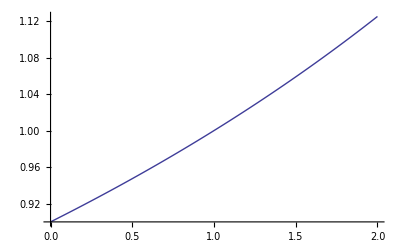

```mathematica
Plot[wR0/(1+(wR0-1) noverK)/.wR0->0.9,{noverK,0,2}]
```

So why work with Beverton-Holt in the first place??  Comparing the logistic and B-H logistic, where both are parameterized such that R0 is growth when rare and K is the steady state:

```mathematica
1+(R0-1)(1-n/K)
```

```mathematica
R0/(1+(R0-1) n/K)
```

What happens to the number of offspring per parent when n is very very very large?

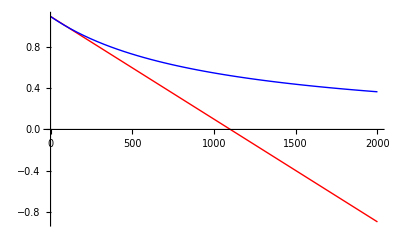

```mathematica
Show[Plot[1+(R0-1)(1-n/K)/.R0->1.1/.K->100,{n,0,2000},PlotStyle->Red],
Plot[R0/(1+(R0-1) n/K)/.R0->1.1/.K->100,{n,0,2000},PlotStyle->Blue]]
```